```mathematica
ClearAll["Global`*"]
```

```mathematica
G=6.67×10^-11;
Mz=5.96×10^24;
```

```mathematica
FG=G×(m×Mz)/R^2;
Fod=(m×v^2)/R
```

(m v^2)/R

```mathematica
r1=Solve[FG==Fod,v]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{v→-(1.99382×10^7)/(√R)},{v→(1.99382×10^7)/(√R)}}

```mathematica
v[R_]=v/.r1[[2,1]];
```

```mathematica
T[R_]=(2×π×R)/v[R];
```

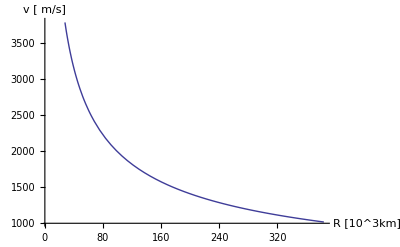

```mathematica
Plot[v[R×10^6],{R,6.370,3.84×10^2},
AxesLabel->{"R  [10^3km]","v [ m/s]"}]
```

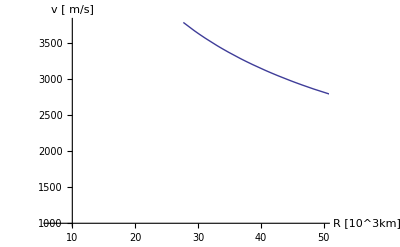

```mathematica
Plot[v[R×10^6],{R,6.370,3.84×10^2},PlotRange->{{6.370,50.000},Automatic},
AxesLabel->{"R  [10^3km]","v [ m/s]"}]
```

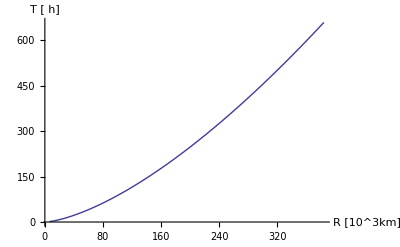

```mathematica
Plot[T[R×10^6]/3600,{R,6.370,3.84×10^2},
AxesLabel->{"R [10^3km]","T [ h]"}]
```

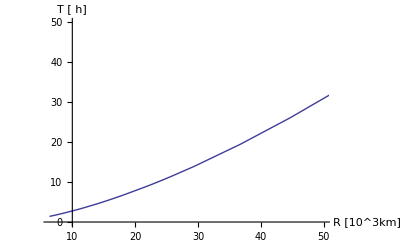

```mathematica
Plot[T[R×10^6]/3600,{R,6.370,3.84×10^2},PlotRange->{{6.370,50.000},{0,50}},
AxesLabel->{"R [10^3km]","T [ h]"}]
```